```mathematica
nMax=4000;
fib[x_,p_,q_,m_]:=RecurrenceTable[
{
X[n]==Mod[X[n-p]+X[n-q],m],
Table[X[i]==x[[i]],{i,1,q}]},
X,
{n,1,nMax}
];
```

```mathematica
modulo = 2^10;
seq = Table[RandomInteger[modulo],{i,1,67}];
fib[x_,p_,q_,m_]:=RecurrenceTable[{X[n]==Mod[X[n-p]+X[n-q],m],Table[X[i]==x[[i]],{i,1,q}]},X,{n,1,nMax}];
```

```mathematica
(**fib[x0,p,q,m];**)
```

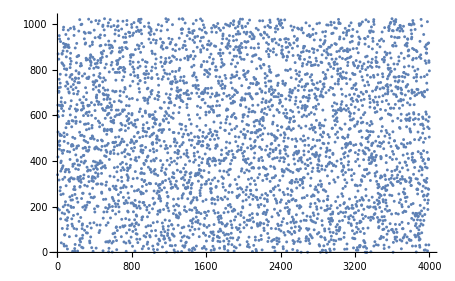
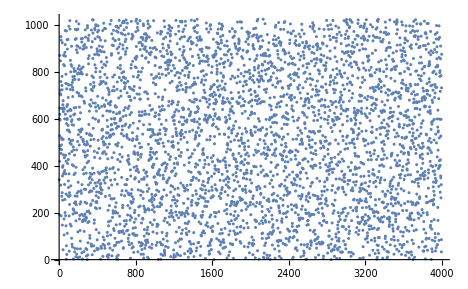
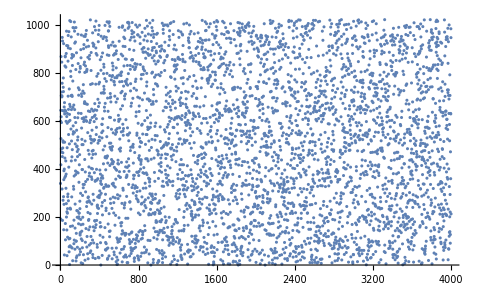
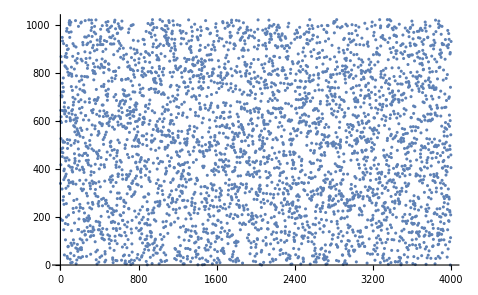
{{{-Graphics-,p=18,q=65},{-Graphics-,p=18,q=66}},{{-Graphics-,p=19,q=65},{-Graphics-,p=19,q=66}}}

```mathematica
Table[{ListPlot[fib[seq,p,q,modulo]],"p="~~ToString[p],"q="~~ToString[q]},{p,18,19},{q,65,66}]
```